# Case Versus Phylogentic Likelihood

```mathematica
col1 = ColorData[97][1]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
col2 = ColorData[97][2]
```

RGBColor[0.880722, 0.611041, 0.142051]

## Global Events

Simulating a tree

```mathematica
increment[Δt_,sVecIn_,treeMtrxIn_]:=Block[{j,sVec,treeMtrx},
{sVec,treeMtrx}={sVecIn,treeMtrxIn};
For[j=1,j≤Length[treeMtrx],j++,
If[sVec[[j]]>0,treeMtrx[[j,j]]+=Δt]
];
{sVec,treeMtrx}
]
```

```mathematica
(*Birth*)
birth[Δt_,sVecIn_,treeMtrxIn_]:=Block[{n,sVec,treeMtrx,temp},
{sVec,treeMtrx}=increment[Δt,sVecIn,treeMtrxIn];
n=RandomChoice[Flatten[Position[sVec,_?(#>0&)]]];
(*Add element to sVec*)
AppendTo[sVec,1];
(*Add row to treeMtrx*)
AppendTo[treeMtrx,treeMtrx[[n]]];
temp=Transpose[treeMtrx];
treeMtrx=Transpose[AppendTo[temp,Join[treeMtrx[[n]],{t}]]];
{sVec,treeMtrx}
]
```

```mathematica
death[Δt_,sVecIn_,treeMtrxIn_]:=Block[{n,sVec,treeMtrx,temp},
{sVec,treeMtrx}=increment[Δt,sVecIn,treeMtrxIn];
n=RandomChoice[Flatten[Position[sVec,_?(#>0&)]]];
(*Change state of lin*)
sVec[[n]]=0;
{sVec,treeMtrx}
]
```

```mathematica
samplingWReplacement[Δt_,sVecIn_,treeMtrxIn_]:=Block[{n,sVec,treeMtrx,temp},
{sVec,treeMtrx}=increment[Δt,sVecIn,treeMtrxIn];
n=RandomChoice[Flatten[Position[sVec,_?(#>0&)]]];
(*Add element to sVec*)
AppendTo[sVec,-1];
(*Add row to treeMtrx*)
AppendTo[treeMtrx,treeMtrx[[n]]];
temp=Transpose[treeMtrx];
treeMtrx=Transpose[AppendTo[temp,Join[treeMtrx[[n]],{t}]]];
{sVec,treeMtrx}
]
```

```mathematica
samplingWOutReplacement[Δt_,sVecIn_,treeMtrxIn_]:=Block[{n,sVec,treeMtrx,temp},
{sVec,treeMtrx}=increment[Δt,sVecIn,treeMtrxIn];
n=RandomChoice[Flatten[Position[sVec,_?(#>0&)]]];
(*Change state of lin*)
sVec[[n]]=-1;
{sVec,treeMtrx}
]
```

```mathematica
samplingρ[Δt_,ρ_,sVecIn_,treeMtrxIn_]:=Block[{nList,sVec,treeMtrx,temp},
{sVec,treeMtrx}={sVecIn,treeMtrxIn};
nList=Flatten[Position[sVec,_?(#>0&)]];
Do[
treeMtrx[[n,n]]+=Δt;
If[RandomReal[]<ρ,sVec[[n]]=-1,sVec[[n]]=0];
,{n,nList}];
{sVec,treeMtrx}
]
```

```mathematica
nearNeighbour[treeMtrx_]:=Block[{UTM,pos},
UTM=UpperTriangularize[treeMtrx,1];
Position[UTM,Max[UTM]][[1]]//Sort
]
```

```mathematica
newick[treeMtrx_]:=Block[{treeTenp,order,l1,l2},
(*Initialize*)
order=Table[x,{x,1,Length[treeMtrx]}];
treeTenp=treeMtrx;
While[Length[treeTenp]>1,
{l1,l2}=nearNeighbour[treeTenp];
(*Update trMtrx and sMtrx*)
Print[{treeTenp[[l1,l1]]-treeTenp[[l1,l2]],treeTenp[[l2,l2]]-treeTenp[[l1,l2]]}];
treeTenp[[l1,l1]]=treeTenp[[l1,l2]];
treeTenp=Delete[treeTenp,l2];
treeTenp=Transpose[Delete[Transpose[treeTenp],l2]];
order[[l1]]=order[[{l1,l2}]];
order=Delete[order,l2];
];
order
];
```

```mathematica
newickText[treeMtrx_]:=Block[{treeTenp,order,l1,l2},
(*Initialize*)
order=Table[ToString[x],{x,1,Length[treeMtrx]}];
treeTenp=treeMtrx;
While[Length[treeTenp]>1,
{l1,l2}=nearNeighbour[treeTenp];
(*Update trMtrx and sMtrx*)
order[[l1]]={"{"<>order[[l1]]<>"}:"<>ToString[treeTenp[[l1,l1]]-treeTenp[[l1,l2]]]<>","<>"{"<>order[[l2]]<>"}:"<>ToString[treeTenp[[l2,l2]]-treeTenp[[l1,l2]]]};
treeTenp[[l1,l1]]=treeTenp[[l1,l2]];
treeTenp=Delete[treeTenp,l2];
treeTenp=Transpose[Delete[Transpose[treeTenp],l2]];
order=Delete[order,l2];
];
order=ToString[order];
order=StringReplace[order,{"{"->"(","}"->")"}];
order=StringReplace[order,Table["("<>ToString[j]<>")"->ToString[j],{j,1,Length[treeMtrx]}]];
order
];
```

```mathematica
sampCt[treeMtrx_,Τ_]:=Block[{treeTenp,fTips,eTips,fAns,,l1,l2},
fTips=0;eTips=0;fAns=0;
eTips=Length[Select[Diagonal[treeMtrx],#==Τ&]];
fTips=Length[treeMtrx]-eTips;
treeTenp=treeMtrx;
While[Length[treeTenp]>1,
{l1,l2}=nearNeighbour[treeTenp];
If[treeTenp[[l2,l2]]-treeTenp[[l1,l2]]==0,fAns++;fTips--];
If[treeTenp[[l1,l1]]-treeTenp[[l1,l2]]==0,fAns++;fTips--];
(*Update trMtrx and sMtrx*)
treeTenp[[l1,l1]]=treeTenp[[l1,l2]];
treeTenp=Delete[treeTenp,l2];
treeTenp=Transpose[Delete[Transpose[treeTenp],l2]];
];
{eTips,fTips,fAns}
]
```

## Simulating SIR Trees

```mathematica
testParsSIR={β->1,κ->100,γ->0.2,ψ->0.4,r->1,ρ->0,Τ->20};
```

```mathematica
Clear[testParsSIR2]
testParsSIR2[intS_]:=testParsSIR2[intS]={β->RandomReal[{0.2,3}],κ->100,γ->0.2,ψ->0.4,r->1,ρ->0,Τ->20};
```

State Vector {t, S, I, R,I*}

```mathematica
ratesSIR[Se_]:={(*transmission*)(β Se[[2]]Se[[3]])/κ,(*recover*)γ Se[[3]],(*sampling w/out removal*)ψ (1-r) Se[[3]],(*samp w removal*)ψ r Se[[3]]};
```

```mathematica
ΔSeSIR[Δt_]:={{Δt,-1,1,0,0},{Δt,0,-1,1,0},{Δt,0,0,0,1},{Δt,0,-1,1,1}}
```

```mathematica
ΔDivSIR[Δt_,e_,sVecIn_,treeMtrxIn_]:=Block[{sVec,treeMtrx},
If[e==1, {sVec,treeMtrx}=birth[Δt,sVecIn,treeMtrxIn],
If[e==2, {sVec,treeMtrx}=death[Δt,sVecIn,treeMtrxIn],
If[e==3, {sVec,treeMtrx}=samplingWReplacement[Δt,sVecIn,treeMtrxIn],
If[e==4, {sVec,treeMtrx}=samplingWOutReplacement[Δt,sVecIn,treeMtrxIn],Print["Error"]]]]];
{sVec,treeMtrx}
]
```

```mathematica
Clear[simSIR,simSIREpi]
simSIR[pars_,intS_]:=simSIR[pars,intS]=Block[{sVec,treeMtrx,Se,t,temp, Δt,e,x},
(*Initialize*)
t=0; Se={{0,κ-1,1,0,0}}/.pars;
sVec={1};treeMtrx={{0}};
(*Firt event*)
temp=ratesSIR[Se[[-1]]]/.pars;
Δt=RandomVariate[ExponentialDistribution[Total[temp]]];
(*For[x=1,x<=2,x++,*)
While[t+Δt<(Τ/.pars),
t=t+Δt;
(*Choose Event*)
e=RandomChoice[temp->{1,2,3,4}];
(*Update State*)
Se=AppendTo[Se,Se[[-1]]+ΔSeSIR[Δt][[e]]];
{sVec,treeMtrx}=ΔDivSIR[Δt,e,sVec,treeMtrx];
(*Choose Next Δt*)
temp=ratesSIR[Se[[-1]]]/.pars;
If[Total[temp]>0,
Δt=RandomVariate[ExponentialDistribution[Total[temp]]],Δt=Τ/.pars];
];
simSIREpi[pars,intS]=Se;
(*Present-day Sampling*)
{sVec,treeMtrx}=samplingρ[Τ-t/.pars,ρ/.pars,sVec,treeMtrx];
{sVec,treeMtrx}
]
```

```mathematica
simSIR[testParsSIR,1];
```

This function is used for retrieving time which we can use it later for curve fitting

```mathematica
simSIREpi2[pars_,intS_]:=Block[{},
simSIR[pars,intS];
simSIREpi[pars,intS]
]
```

```mathematica
simSIREpi2[testParsSIR2[7],7]
```

{{0,99,1,0,0},{0.603393,99,0,1,1}}

```mathematica
smpOut = 3
```

3

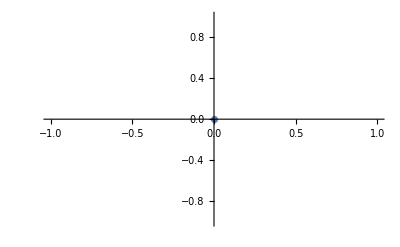

```mathematica
Transpose[{simSIREpi2[testParsSIR2[smpOut],smpOut][[;;,1]],Log[simSIREpi2[testParsSIR2[smpOut],smpOut]][[;;,3]]}]//ListPlot
```

```mathematica
simSIREpi2[testParsSIR2[smpOut],smpOut][[;;,3]]
```

{1,0}

Creating the sampled tree.

```mathematica
(*List of Lineages in the sampled tree*)
sampTreeSIR[pars_,intS_]:=Block[{linList},
linList=Flatten[Position[simSIR[pars,intS][[1]],_?(#==-1&)]];
simSIR[pars,intS][[2]][[linList,linList]]]
```

```mathematica
sampTreeSIR[testParsSIR2[smpOut],smpOut];
```

```mathematica
yVec[pars_,intS_]:=(Τ/.pars)-Diagonal[sampTreeSIR[pars,intS]]
xVec[pars_,intS_]:=(Τ/.pars)-DeleteDuplicates[DeleteCases[Flatten[UpperTriangularize[sampTreeSIR[pars,intS],1]],0.]]
```

```mathematica
cVec[pars_,intS_]:=Diagonal[sampTreeSIR[pars,intS]]
```

```mathematica
yVec[testParsSIR,smpOut];
```

```mathematica
cVec[testParsSIR,smpOut];
```

```mathematica
testTreeList=Flatten[Position[Table[Length[cVec[testParsSIR2[j],j]],{j,1,100}],_?(#>1&)]];
```

```mathematica
testTreeList
```

{1,2,5,6,10,11,12,14,15,16,19,20,21,23,24,26,28,30,31,32,34,35,37,38,40,43,45,47,48,49,51,52,54,55,57,59,60,61,62,65,66,67,68,69,71,76,79,82,84,85,87,88,92,93,94,95,96,97,98,99}

```mathematica
smp = 2
```

2

```mathematica
simSIREpi2[testParsSIR2[smp],smp];
```

```mathematica
outputDirectory="/Users/siavashriazi/Desktop/SFU/beast_alignments/mathematica_results/SIR_files";
```

```mathematica
Do[dynamics=simSIREpi2[testParsSIR2[i],i];(*Get SIR dynamics*)If[MemberQ[testTreeList,i],Export[FileNameJoin[{outputDirectory,ToString[i]<>"_SIR.csv"}],dynamics,"CSV"]],{i,Max@testTreeList}]
```

```mathematica
sampTreeSIR[testParsSIR2[smp],smp];
```

```mathematica
newick[sampTreeSIR[testParsSIR2[smp],smp]]
```

{2.77182,1.11485}

{5.71283,0.0898272}

{1.36604,0.659832}

{1.24248,1.03408}

{2.03061,0.766411}

{1.24642,1.1269}

{0.21457,0.865711}

{1.52569,0.851426}

{1.28156,0.590736}

{0.0592044,0.963452}

{0.24658,4.69308}

{2.667,0.249837}

{0.160211,3.1436}

{0.672212,1.52304}

{1.64968,3.08456}

{0.0951415,1.95866}

{0.134457,0.42396}

{0.268156,1.18842}

{0.159182,1.5927}

{0.0316724,0.318644}

{0.709515,0.531656}

{0.424329,0.429004}

{0.444785,0.0410321}

{0.0738059,1.30366}

{0.0802313,0.451721}

{0.239172,0.589618}

{1.1145,1.31536}

{0.24961,0.766616}

{0.70027,0.285658}

{1.02048,0.858179}

{0.309151,0.00556872}

{0.0148528,0.19518}

{1.89005,1.13852}

{0.850614,3.56655}

{0.0502099,1.97411}

{1.1227,0.637214}

{0.707722,1.66611}

{0.239044,0.72061}

{0.0558976,3.17509}

{0.129621,0.295211}

{0.533156,1.98184}

{0.371814,0.103655}

{0.278454,0.991878}

{0.998045,0.863754}

{0.276007,0.0277781}

{0.00836169,1.12824}

{1.81017,0.258986}

{0.0185377,0.43825}

{0.237519,0.95447}

{0.172862,0.0130904}

{0.0672995,0.616042}

{0.0409765,0.72432}

{0.867877,0.557806}

{0.0190259,0.0372856}

{0.309687,0.333647}

{0.0456487,0.225367}

{0.121582,0.465899}

{{1,{{2,{{4,{{10,25},14}},{{8,{{12,20},{{13,33},{29,{39,41}}}}},{9,21}}}},{{{{3,{45,{48,49}}},17},{6,{11,36}}},{{5,{{{18,40},{{{28,52},31},{46,{51,53}}}},{32,{43,{57,58}}}}},{{{{7,27},{23,24}},{{{22,{{{30,{44,54}},{37,{{42,{55,56}},50}}},34}},{38,47}},26}},{{{15,19},35},16}}}}}}}

```mathematica
data = simSIREpi2[testParsSIR2[testTreeList[[1]]],testTreeList[[1]]][[All,{1,3}]];
```

```mathematica
outputDirectory="/Users/siavashriazi/Desktop/SFU/Codes/simulations/";
```

```mathematica
outputFileName="sim"<>IntegerString[testTreeList[[1]]]<>".csv";
```

```mathematica
outputFilePath=FileNameJoin[{outputDirectory,outputFileName}];
```

```mathematica
Export[outputFilePath,data,"CSV"]
```

/Users/siavashriazi/Desktop/SFU/Codes/simulations/sim3.csv

```mathematica
Do[data=simSIREpi2[testParsSIR2[testTreeList[[i]]],testTreeList[[i]]][[All,{1,3}]];
outputFileName="sim"<>IntegerString[testTreeList[[i]]]<>".csv";
outputFilePath=FileNameJoin[{outputDirectory,outputFileName}];
Export[outputFilePath,data,"CSV"],{i,1,Length[testTreeList]}]
```

```mathematica
cVec[testParsSIR2[33],33];
```

```mathematica
treeSize[intS_]:=Length[cVec[testParsSIR2[intS],intS]]
```

```mathematica
treeSize/@ testTreeList
```

{613,642,657,639,627,644,642,9,2,643,119,616,636,653,646,615,600,2,650,621,598,460,643,2,660,683,651,2,546,659,16,539,641,406,641,608,504,620,567,677,6,136,681,653,660,8,579,646,2,530,655,661,668,571,605,619,457,394,586}

## Case Likelihood

## Numerical Integrate SIR

```mathematica
odes={D[x[t],t]==-β/κ x[t]y[t],D[y[t],t]==β/κ x[t]y[t]-(γ+ψ r) y[t],D[z[t],t]==(γ+ψ r)y[t]};
vars={x[t],y[t],z[t]};
inits={x[0]==κ-1,y[0]==1,z[0]==0};
Clear[nSIR]
nSIR[pars_]:=nSIR[pars]=NDSolve[Join[odes,inits]/.pars,vars,{t,0,Τ/.pars}][[1]]
nSsol[pars_,t2_]:=x[t]/.nSIR[pars]/.t->t2
nIsol[pars_,t2_]:=y[t]/.nSIR[pars]/.t->t2
nRsol[pars_,t2_]:=z[t]/.nSIR[pars]/.t->t2
```

```mathematica
nIsol[testParsSIR,20]
```

57.8186

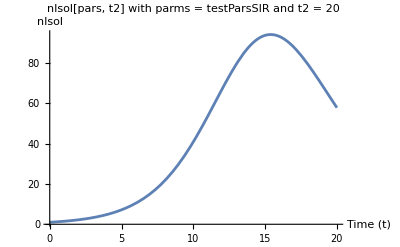

```mathematica
Plot[nIsol[testParsSIR,20],{t,0,20},PlotLabel->"nIsol[pars, t2] with parms = testParsSIR and t2 = 20",AxesLabel->{"Time (t)","nIsol"},PlotRange->All]
```

```mathematica
testParsSIR
```

```mathematica
{β->1,κ->1000,γ->0.2,ψ->0.4,r->1,ρ->0,Τ->20}
```

{β→1,κ→1000,γ→0.2,ψ→0.4,r→1,ρ→0,Τ→20}

```mathematica
Idata=Table[{t,nIsol[testParsSIR,t]},{t,0,20}]
```

{{0,1.},{1,1.48948},{2,2.21521},{3,3.2872},{4,4.86185},{5,7.15588},{6,10.4577},{7,15.1264},{8,21.5605},{9,30.1076},{10,40.8883},{11,53.5441},{12,67.0084},{13,79.5051},{14,88.9553},{15,93.7014},{16,93.1351},{17,87.8274},{18,79.1461},{19,68.6841},{20,57.8186}}

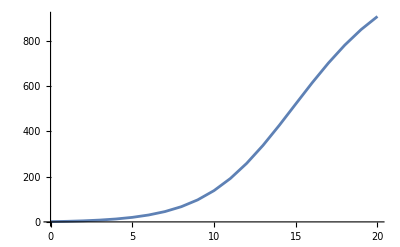

```mathematica
Iaccudata=Transpose[{Idata[[All,1]],Accumulate[Idata[[All,2]]]}]//ListLinePlot
```

## Calculate Likelihood

where

First, lets deal with the integral.

 
Note that

```mathematica
Clear[Ω]
Ω[pars_]:=Ω[pars]=Block[{tab,Δt},
Δt=Τ/100/.pars;
tab=Table[{Δt,Δt (ψ/.pars) nIsol[pars,t2]},{t2,0,Τ/.pars,Δt}];
tab=Join[{{0,0}},Accumulate[tab]];
Interpolation[tab]
]
```

Calculating the probability of observing a case:

```mathematica
PrC[j_,cVec_,pars_]:=(ψ /.pars)nIsol[pars,cVec[[j]]] Exp[-(Ω[pars][cVec[[j]]]-Ω[pars][If[j==1,0,cVec[[j-1]]]])]
```

Calculating the likelihood of observing a case:

```mathematica
ℒCase[cVec_,pars_]:=Product[PrC[j,cVec,pars],{j,1,Length[cVec]}]
```

#### Conditioning

Conditioning of the likelihood we need to multiply the likelihood by:

Where C(0) is probability of observing no case

```mathematica
𝒞[pars_]:=1-Exp[-Ω[pars][Τ/.pars]]
```

```mathematica
ℒCaseCond[cVec_,pars_]:=Product[PrC[j,cVec,pars],{j,1,Length[cVec]}]/𝒞[pars]
```

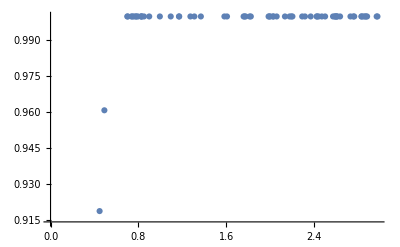

```mathematica
Table[{β/.testParsSIR2[intS],𝒞[testParsSIR2[intS]]},{intS,testTreeList}]//ListPlot
```

### Testing

Recall that the true parameters are...

```mathematica
likPars[βin_]=Join[{β->βin},testParsSIR[[2;;]]];
```

The likelihood surface

```mathematica
Clear[ℒCList]
ℒCList[intS_]:=ℒCList[intS]=Block[{cVecTest,out,Δβ,temp},
cVecTest=cVec[testParsSIR2[intS],intS];
Δβ=0.02;
If[Length[cVecTest]==0,out="No Tree",
out=Table[{β,ℒCaseCond[cVecTest,likPars[β]]},{β,0.8,3,Δβ}];
temp=Total[out[[;;,2]]Δβ];
out=Map[{#[[1]],(#[[2]])/temp}&,out];
];
out
]
```

General::munfl: 2.55204×10^-35 4.26413303239305×10^-989 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.85565×10^-13 4.26413303239305×10^-989 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.04396×10^10 4.26413303239305×10^-989 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

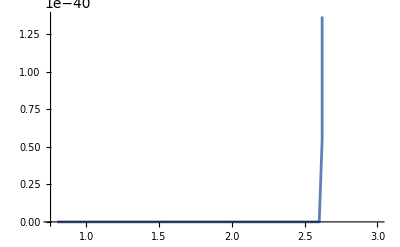

```mathematica
ListLinePlot[ℒCList[33]]
```

Calculating maximum posterior estimate of case likelihood

```mathematica
ℒCMPE[intS_]:=Block[{cVecTest,out,temp},
cVecTest=cVec[testParsSIR2[intS],intS];
If[Length[cVecTest]==0,out="No Tree",
out=Sort[ℒCList[intS],#1[[2]]>#2[[2]]&][[1,1]];
];
out
]
```

Calculating confidence interval of case likelihood

```mathematica
ℒCCI[intS_]:=Block[{cVecTest,out,temp,temp2,temp3,Δβ,ℒInt},
cVecTest=cVec[testParsSIR2[intS],intS];
If[Length[cVecTest]==0,out="No Tree",
(*Extract the Δβ step*)
Δβ=ℒCList[intS][[2,1]]-ℒCList[intS][[1,1]];
(*Convert Probilibty densities into probability by dividing the PDF into Δβ steps*)
temp=Map[{#[[1]],#[[2]]Δβ}&,ℒCList[intS]];
(*Sort the probabilities*)
temp=Sort[temp,#1[[2]]>#2[[2]]&];
(*Integrate the probabilites*)
temp2=Transpose[{temp[[;;,1]],Accumulate[temp[[;;,2]]]}];
(*β Values in the CI*)
temp3=Select[temp2,#[[2]]<0.95&][[;;,1]];
out=temp3
];
out
]
```

General::munfl: 0.02 1.9100222550253×10^-673 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 2.97212979775588×10^-656 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.28913326363866×10^-639 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

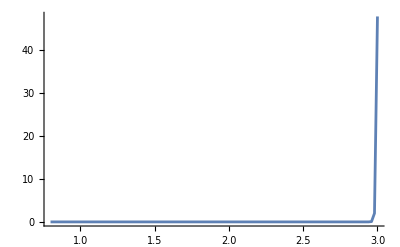

```mathematica
Show[ListLinePlot[ℒCList[33],PlotRange->All],ListLinePlot[Map[{#,0.5}&,ℒCCI[33]]],PlotRange->All]
```

## Phylogenetic Likelihood

```mathematica
λ[τ_,pars_]:=(β/κ/.pars)nSsol[pars,(Τ/.pars)-τ]
```

```mathematica
Clear[nEsol]
```

```mathematica
Clear[nsolE]
nsolE[pars_]:=nsolE[pars]=NDSolve[{D[e[τ],τ]==-(λ[τ,pars]+γ+ψ)e[τ]+λ[τ,pars] e[τ]^2+γ/.pars,e[0]==1},e[τ],{τ,0,Τ/.pars}][[1]]
nEsol[τ2_,pars_]:=e[τ]/.nsolE[pars]/.τ->τ2
```

```mathematica
Clear[ΦArg]
ΦArg[pars_]:=ΦArg[pars]=Block[{tab,Δt},
Δt=Τ/100/.pars;
tab=Table[{Δt,Δt (-((λ[t2,pars]+γ+ψ)/.pars)+2λ[t2,pars]nEsol[t2,pars])},{t2,0,Τ/.pars,Δt}];
tab=Join[{{0,0}},Accumulate[tab]];
Interpolation[tab]
]
```

```mathematica
Φ[τ_,pars_]:=Exp[ΦArg[pars][τ]]
```

Calculating likelihood of phylogeny:

```mathematica
ℒPhy[xVec_,yVec_,pars_]:=Block[{out,i,j},
out=Φ[Τ/.pars,pars];
For[i=1,i<=Length[xVec],i++,
out*=λ[xVec[[i]],pars]Φ[xVec[[i]],pars]
];
For[j=1,j<=Length[yVec],j++,
out*=(ψ/.pars)/Φ[yVec[[j]],pars]
];
out
]
```

## Conditioning on Phylogeny

To condition the likelihood we need to multiply by:

```mathematica
ℒPhyCond[xVec_,yVec_,pars_]:=Block[{out,i,j,denominator},out=Φ[Τ/. pars,pars];
For[i=1,i<=Length[xVec],i++,out*=λ[xVec[[i]],pars] Φ[xVec[[i]],pars]];
For[j=1,j<=Length[yVec],j++,out*=(ψ/. pars)/Φ[yVec[[j]],pars];];
denominator=1-nEsol[(Τ/. pars),pars];
out/denominator]
```

```mathematica
LogℒPhy[xVec_,yVec_,pars_]:=Block[{out,i,j},
out=ΦArg[pars][Τ/.pars];
For[i=1,i<=Length[xVec],i++,
out+=Log[λ[xVec[[i]],pars]]+ΦArg[pars][xVec[[i]]]
];
For[j=1,j<=Length[yVec],j++,
out+=Log[ψ/.pars]-ΦArg[pars][yVec[[j]]]
];
out
]
```

```mathematica
LogℒPhy2[intS_,pars_]:=LogℒPhy[xVec[testParsSIR2[intS],intS],yVec[testParsSIR2[intS],intS],pars]
```

```mathematica
LogℒPhyCond[xVec_,yVec_,pars_]:=Block[{out,i,j,denom},
out=ΦArg[pars][Τ/.pars];
For[i=1,i<=Length[xVec],i++,
out+=Log[λ[xVec[[i]],pars]]+ΦArg[pars][xVec[[i]]]
];
For[j=1,j<=Length[yVec],j++,
out+=Log[ψ/.pars]-ΦArg[pars][yVec[[j]]]
];
denom=Log[1-nEsol[(Τ/. pars),pars]];
out=out-denom
]
```

```mathematica
LogℒPhyCond2[intS_,pars_]:=LogℒPhyCond[xVec[testParsSIR2[intS],intS],yVec[testParsSIR2[intS],intS],pars]
```

Creating a list of phylogeny likelihood:

```mathematica
Clear[ℒPList]
ℒPList[intS_]:=ℒPList[intS]=Block[{xVecTest,yVecTest,out,Δβ,temp,min},
xVecTest=xVec[testParsSIR2[intS],intS];
yVecTest=yVec[testParsSIR2[intS],intS];
Δβ=0.02;
If[Length[yVecTest]==0,out="No Tree",
out=Table[{β,LogℒPhyCond[xVecTest,yVecTest,likPars[β]]},{β,0.8,3,Δβ}];
out=Transpose[{out[[;;,1]],out[[;;,2]]}];
min=out[[;;,2]]//Min;
out=Map[{#[[1]],#[[2]]-min}&,out];
temp=Total[out[[;;,2]]Δβ];
out=Map[{#[[1]],(#[[2]])/temp}&,out];
];
out
]
```

Calculating maximum posterior estimate of phylogeny likelihood:

```mathematica
ℒPMPE[intS_]:=Block[{yVecTest,out},
yVecTest=yVec[testParsSIR2[intS],intS];
If[Length[yVecTest]==0,out="No Tree",
out=Sort[ℒPList[intS],#1[[2]]>#2[[2]]&][[1,1]]];
out
]
```

```mathematica
ℒPMPE[1]
```

No Tree

Calculating confidence interval of phylogeny likelihood:

```mathematica
ℒPCI[intS_]:=Block[{yVecTest,out,temp,temp2,temp3,Δβ,ℒInt},
yVecTest=yVec[testParsSIR2[intS],intS];
If[Length[yVecTest]==0,out="No Tree",
Δβ=ℒPList[intS][[2,1]]-ℒPList[intS][[1,1]];
temp=Map[{#[[1]],#[[2]]Δβ}&,ℒPList[intS]];
temp=Sort[temp,#1[[2]]>#2[[2]]&];
temp2=Transpose[{temp[[;;,1]],Accumulate[temp[[;;,2]]]}];
(*β Values in the CI*)
out=Select[temp2,#[[2]]<0.95&][[;;,1]];
];
out
]
```

```mathematica
Show[ℒPList[1]//ListLinePlot,ListPlot[Map[{#,0.005}&,ℒPCI[1]]]]
```

UpperTriangularize::matrix: Argument {} at position 1 is not a non-empty rectangular matrix.

ListLinePlot::lpn: No Tree is not a list of numbers or pairs of numbers.

ListPlot::lpn: No Tree is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[No Tree],ListPlot[No Tree]].

Show[ListLinePlot[No Tree],ListPlot[No Tree]]

## Comparing Case and Phylo

Calculating a likelihood surface for phylogeny and case counts given a tree

```mathematica
CompPlot[intS_]:=ListLinePlot[{ℒCList[intS],ℒPList[intS]},PlotRange->All]
```

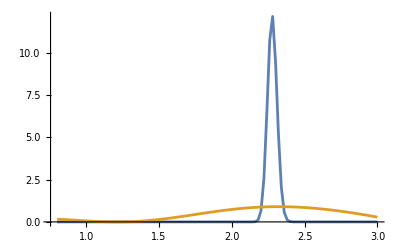

```mathematica
CompPlot[3]
```

```mathematica
CompPlot[intS_]:=Module[{betaValue},betaValue=β/. testParsSIR2[intS];
ListLinePlot[{ℒCList[intS],ℒPList[intS]},PlotRange->All,Epilog->{Red,Line[{{betaValue,0},{betaValue,5.5}}]}]]
```

```mathematica
testTreeList
```

{3,4,7,8,11,12,14,16,17,19,21,22,23,24,25,27,29,30,33,37,38,39,40,42,43,45,46,47,48,49,50,51,52,54,57,58,60,61,63,68,70,73,74,75,76,79,80,81,84,86,87,88,89,90,92,93,94,96,99}

General::munfl: 3.74687×10^40 2.39219496312479×10^-1011 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.32588×10^70 2.39219496312479×10^-1011 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.02993×10^99 2.39219496312479×10^-1011 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

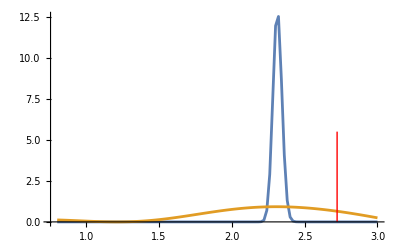

```mathematica
CompPlot[7]
```

General::munfl: 9128.67 4.11487986230137×10^-966 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.19004×10^29 4.11487986230137×10^-966 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.18433×10^54 4.11487986230137×10^-966 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

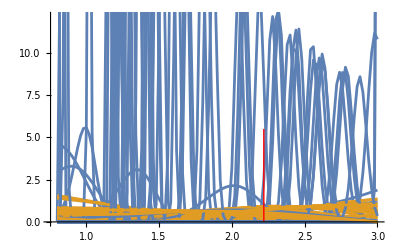

```mathematica
Show[Table[CompPlot[testTree],{testTree,testTreeList}]]
```

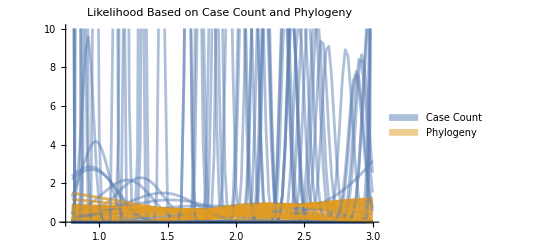

```mathematica
CompPlot[intS_List]:=Table[ListLinePlot[{ℒCList[testTree],ℒPList[testTree]},PlotRange->{Automatic,{0,10}},PlotStyle->{Directive[Opacity[0.5],col1],Directive[Opacity[0.5],col2]},PlotLabel->"Likelihood Based on Case Count and Phylogeny",FrameLabel->{"","Likelihood"}],{testTree,intS}];

legend=SwatchLegend[{Directive[Opacity[0.5],col1],Directive[Opacity[0.5],col2]},{"Case Count","Phylogeny"}];

Legended[Show[CompPlot[testTreeList]],Placed[legend,Right]]
```

plotting confidence interval and maximum posterior estimate for case counts and phylogeny likelihood per given tree

```mathematica
leg=PointLegend[{ColorData[97][1],ColorData[97][2],Red},{"Case","Phylo","Truth"}];
CICompPlot[intS_]:=Block[{βTrue},
βTrue=β/.testParsSIR2[intS];
Show[
(*Credible Intervals*)
ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]],Map[{#,βTrue}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->{Directive[ColorData[97][1],Opacity[0.3]],Directive[ColorData[97][2],Opacity[0.3]]}],
(*Maximum Posterior Estimates*)
ListPlot[{{{βTrue,ℒCMPE[intS]}},{{ℒPMPE[intS],βTrue}},{{βTrue,βTrue}}},PlotMarkers->{Automatic, Medium},PlotStyle->{Automatic,Automatic,Red}],
PlotRange->{{0.8,3},{0.8,3}},Epilog->Inset[leg,Scaled[{0.9,0.12}]],Frame->True,Axes->False,FrameLabel->{" Phylogeny"," Case"},LabelStyle->Directive[Black, Medium]]]
```

```mathematica
Length[testTreeList]
```

65

maxn shows how many points do we want to show

```mathematica
maxn = 50
```

50

```mathematica
Show[Table[CICompPlot[testTreeList[[j]]],{j,1,Length[testTreeList]}]];
```

General::munfl: 0.02 3.45222630642746×10^-571 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 6.20538548440999×10^-551 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.3769003080043×10^-531 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ListLinePlot::lpn: {{},{{3.,2.97238},{2.98,2.97238},{2.96,2.97238},{2.94,2.97238},{2.92,2.97238},{2.9,2.97238},{2.88,2.97238},{2.86,2.97238},{2.84,2.97238},{2.82,2.97238},«60»}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[«1»].

ListLinePlot::lpn: {{},{{0.8,0.775208},{0.82,0.775208},{0.84,0.775208},{0.86,0.775208},{0.88,0.775208},{0.9,0.775208},{0.92,0.775208},{0.94,0.775208},{0.96,0.775208},{0.98,0.775208},«73»}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[«1»].

Show::gcomb: Could not combine the graphics objects in ….

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

```mathematica
(*Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/scatter.png",%]*)
```

```mathematica
testTreeList
```

{2,3,4,5,6,7,8,12,13,15,16,17,18,19,22,23,32,33,38,39,40,42,46,47,49,50,51,52,53,54,55,56,58,60,61,62,64,66,67,70,72,73,74,75,78,79,80,81,83,84,85,87,88,89,90,91,92,94,95,96,98}

```mathematica
observation = 5
```

5

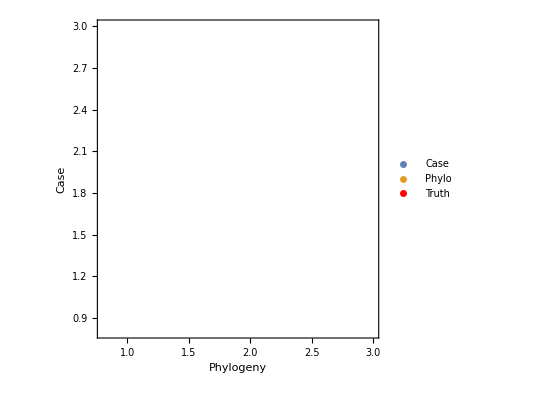

```mathematica
CICompPlot[observation]
```

plotting confidence interval and maximum posterior estimate for case counts and phylogeny likelihood per given tree

```mathematica
(*Clear[testParsSIR2]
testParsSIR2[intS_]:=testParsSIR2[intS]={β->RandomReal[{0.2,3}],κ->100,γ->0.2,ψ->0.4,r->1,ρ->0,Τ->20};*)
```

```mathematica
(*testTreeList=Flatten[Position[Table[Length[cVec[testParsSIR2[j],j]],{j,1,100}],_?(#>1&)]];*)
```

```mathematica
legCICase=PointLegend[{col1,Red},{"Case","Truth"}];
CICasePlot[intS_]:=Block[{βTrue},
βTrue=β/.testParsSIR2[intS];
Show[
(*Credible Intervals*)
ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->{Directive[col1,Opacity[0.3]]}],
(*Maximum Posterior Estimates*)
ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Automatic, Medium},PlotStyle->{Automatic}],
ListPlot[{{{βTrue,βTrue}}},PlotMarkers->{Automatic, Medium},PlotStyle->{Red}],
PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,Epilog->Inset[legCICase,Scaled[{0.1,0.9}]],FrameLabel->{" True","  Case"},LabelStyle->Directive[Black, Medium]]]
```

General::munfl: 0.02 3.45222630642746×10^-571 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 6.20538548440999×10^-551 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.3769003080043×10^-531 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

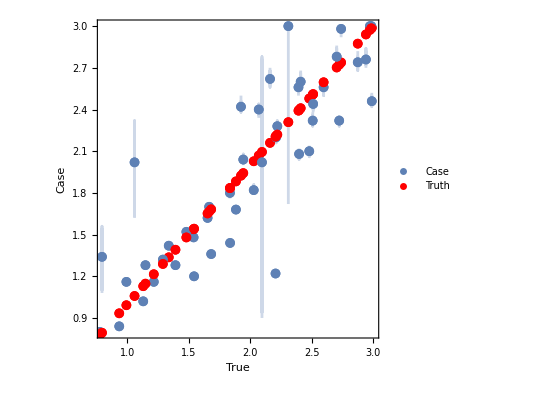

```mathematica
Show[Table[CICasePlot[testTreeList[[j]]],{j,1,maxn(*Length[testTreeList]*)}]]
```

General::munfl: 0.02 3.26177317130724×10^-687 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 5.13350366274614×10^-667 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.54830399466117×10^-647 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

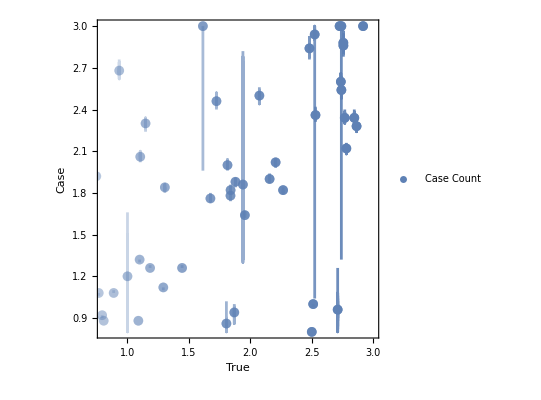

```mathematica
legCICase=PointLegend[{ColorData[97][1]},{"Case Count"}];

CICasePlot[intS_]:=Block[{βTrue},βTrue=β/. testParsSIR2[intS];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->Directive[ColorData[97][1],Opacity[Abs[βTrue]/3]]],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->{Directive[ColorData[97][1],Opacity[Abs[βTrue]/3]]}],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Epilog->Inset[legCICase,Scaled[{0.85,0.12}]],Frame->True,Axes->False,FrameLabel->{" True","  Case"},LabelStyle->Directive[Black,Medium]]]

Show[Table[CICasePlot[testTreeList[[j]]],{j,1,maxn}]]
```

General::munfl: 0.02 3.26177317130724×10^-687 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 5.13350366274614×10^-667 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.54830399466117×10^-647 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

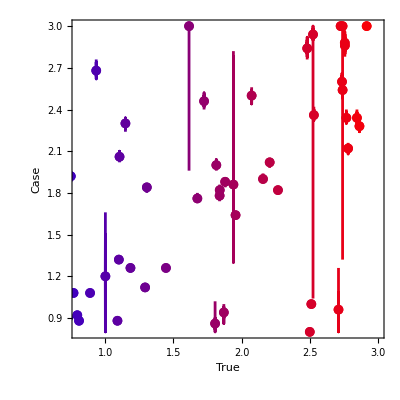

```mathematica
CICasePlot[intS_]:=Block[{βTrue},βTrue=β/. testParsSIR2[intS];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[Blend[{Blue,Red},Abs[βTrue]/3],Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->(Directive[Blend[{Blue,Red},Abs[βTrue]/3],Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Case"},LabelStyle->Directive[Black,Medium]]]

Show[Table[CICasePlot[testTreeList[[j]]],{j,1,maxn}]]
```

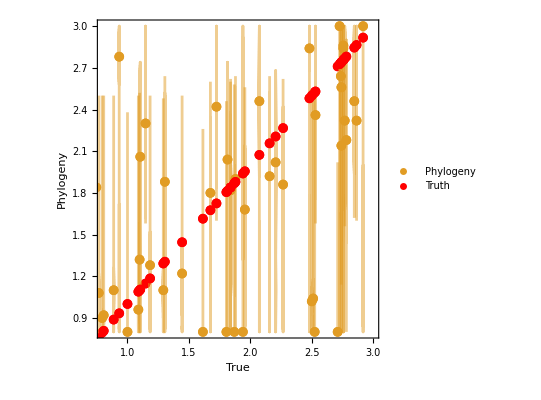

```mathematica
legCIPhylo=PointLegend[{col2,Red},{"Phylogeny","Truth"}];

CICasePlot[intS_]:=Block[{βTrue},βTrue=β/. testParsSIR2[intS];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒPMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->Directive[col2]],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->{Directive[col2,Opacity[0.5]]}],
ListPlot[{{{βTrue,βTrue}}},PlotMarkers->{Automatic, Medium},PlotStyle->{Red}],
AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Epilog->Inset[legCIPhylo,Scaled[{0.12,0.92}]],Frame->True,Axes->False,FrameLabel->{" True","  Phylogeny"},LabelStyle->Directive[Black,Medium]]]

Show[Table[CICasePlot[testTreeList[[j]]],{j,1,maxn}]]
```

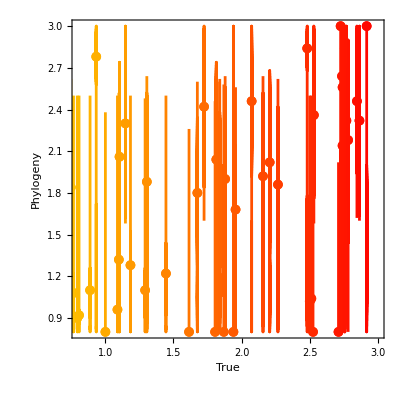

```mathematica
legCIPhyloPlot[intS_]:=Block[{βTrue},βTrue=β/. testParsSIR2[intS];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒPMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[Blend[{Yellow,Red},Abs[βTrue]/3],Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->(Directive[Blend[{Yellow,Red},Abs[βTrue]/3],Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Phylogeny"},LabelStyle->Directive[Black,Medium]]]

Show[Table[legCIPhyloPlot[testTreeList[[j]]],{j,1,maxn}]]
```

```mathematica
cVec[testParsSIR2[observation],observation]
```

{4.5382,0.988089,0.49706,0.907479,0.863989,1.38816,2.90779,1.33811,1.38151,2.13816,1.44166,1.00966,5.01773,1.25519,5.59794,1.33389,2.26739,3.24009,1.55255,2.32015,2.17748,2.73997,4.04817,9.86595,2.02247,2.85477,3.3861,2.22713,6.90729,4.47561,2.31355,3.44849,3.57526,4.00444,4.80214,8.08115,3.27601,4.13604,2.99302,5.73107,3.8675,3.83542,4.58454,3.60536,4.09168,4.2194,7.05944,3.65717,9.29269,5.02026,5.74967,5.00825,6.78446,5.14068,8.62}

```mathematica
treeSize[observation]
```

2

```mathematica
testTreeList
```

{4,7,8,10,11,16,20,22,25,26,30,31,32,33,34,35,36,37,38,42,43,45,51,52,53,56,57,60,61,62,63,64,68,69,70,71,72,74,77,79,81,87,88,89,90,91,95,96,98,99}

```mathematica
treeSize[testTreeList[[8]]]
```

580

33

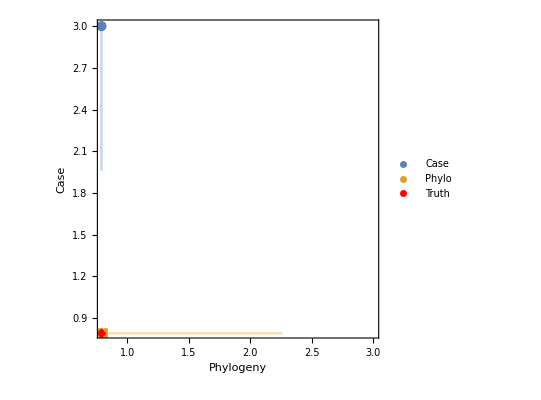

```mathematica
observation =33
CICompPlot[observation]
```

```mathematica
cVec[testParsSIR2[observation],observation]
```

{0.183586}

```mathematica
treeSize[intS_]:=Length[cVec[testParsSIR2[intS],intS]]
```

```mathematica
treeSize[observation]
```

0

## Correlation

Calculating correlation of case counts posterior estimate

```mathematica
dataCMPE=Table[{β/. testParsSIR2[testTreeList[[j]]],ℒCMPE[testTreeList[[j]]]},{j,1,Length[testTreeList]}];
```

```mathematica
correlationCMPE=Correlation[dataCMPE[[All,1]],dataCMPE[[All,2]]]
```

0.758971

Calculating correlation of phylogeny posterior estimate

```mathematica
dataPMPE=Table[{ℒPMPE[testTreeList[[j]]],β/. testParsSIR2[testTreeList[[j]]]},{j,1,Length[testTreeList]}];
```

```mathematica
correlationPMPE=Correlation[dataPMPE[[All,1]],dataPMPE[[All,2]]]
```

0.948057

## Coverage

Calculating two lists that show 1 for hitting the truth and 0 for failing.

```mathematica
CoverageFunction[true_,{lower_,upper_}]:=If[lower<=true<=upper,1,0]
```

```mathematica
CaseCoverageList=Table[CoverageFunction[β/. testParsSIR2[testTreeList[[j]]],{Min[ℒCCI[testTreeList[[j]]]],Max[ℒCCI[testTreeList[[j]]]]}],{j,1,50}];
```

General::munfl: 0.02 5.48452930594082×10^-775 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.71437416661019×10^-751 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.43220533668673×10^-728 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
PhyloCoverageList=Table[CoverageFunction[β/. testParsSIR2[testTreeList[[j]]],{Min[ℒPCI[testTreeList[[j]]]],Max[ℒPCI[testTreeList[[j]]]]}],{j,1,50}];
```

```mathematica
CaseCoverageProbability=N[Total[CaseCoverageList]/maxn]
```

0.12

```mathematica
PhyloCoverageProbability=N[Total[PhyloCoverageList]/maxn]
```

0.86

## Outputing CI into dataframe

```mathematica
betaTrue[intS_]:=β/.testParsSIR2[intS]
```

```mathematica
simulationValues=testTreeList;
```

```mathematica
treeSizeValues=treeSize/@testTreeList;
```

```mathematica
mpeValues=ℒCMPE/@testTreeList;
```

```mathematica
lowerCIValues=Min/@ℒCCI/@testTreeList;
```

```mathematica
upperCIValues=Max/@ℒCCI/@testTreeList;
betaTrueValues = betaTrue/@testTreeList
```

General::munfl: 0.02 3.45222630642746×10^-571 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 6.20538548440999×10^-551 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.3769003080043×10^-531 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{2.21933,2.87377,2.72277,2.40947,1.94249,2.39161,2.73831,0.653823,2.30903,2.06857,0.933781,1.88283,1.83543,1.66488,2.16014,1.68155,1.65226,0.606903,2.97238,2.20977,1.53857,0.991888,2.98791,0.452743,2.98397,2.50738,2.47911,0.334974,1.33654,2.94014,0.775208,1.21481,1.83421,1.1288,2.20497,1.47961,1.147,2.02775,1.54244,2.70247,0.793584,0.713146,2.59608,1.92395,2.51094,1.05831,1.39098,2.39646,2.09472,1.28878,2.16774,2.43878,2.68035,1.37796,1.55662,1.73017,0.986142,1.07251,1.59282}

```mathematica
newdata = {simulationValues,treeSizeValues,betaTrueValues,mpeValues,lowerCIValues,upperCIValues};
```

```mathematica
outputFilePath=FileNameJoin[{outputDirectory,"mathematica.csv"}];
transposedData=Transpose[newdata];
Export[outputFilePath,transposedData,"CSV"]
```

/Users/siavashriazi/Desktop/SFU/Codes/simulations/mathematica.csv

```mathematica
(*Create the DataFrame*)dataFrame=Dataset[<|"Simulation"->simulationValues,"Tree Size"->treeSizeValues,"MPE"->mpeValues,"Lower CI"->lowerCIValues,"Upper CI"->upperCIValues|>]
```

```mathematica
transposedDataFrame=Transpose[dataFrame];
```

## Precision

```mathematica
testTreeList
```

{4,7,8,10,11,16,20,22,25,26,30,31,32,33,34,35,36,37,38,42,43,45,51,52,53,56,57,60,61,62,63,64,68,69,70,71,72,74,77,79,81,87,88,89,90,91,95,96,98,99}

```mathematica
CIWidth[{lower_,upper_}]:=upper-lower
```

```mathematica
CaseWidths=Table[CIWidth[{Min[ℒCCI[testTreeList[[j]]]],Max[ℒCCI[testTreeList[[j]]]]}],{j,1,maxn}]
```

General::munfl: 0.02 5.48452930594082×10^-775 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.71437416661019×10^-751 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.43220533668673×10^-728 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{0.14,0.12,0.14,0.1,0.08,0.1,0.12,0.02,0.,0.02,0.04,0.46,0.06,1.04,0.08,0.06,0.06,0.,1.52,0.12,0.02,0.08,0.06,0.,0.12,0.02,0.06,0.14,0.1,0.02,0.1,0.1,0.02,0.,1.68,1.46,0.1,-∞,0.02,0.12,0.02,1.14,0.04,0.06,0.02,0.02,0.02,0.14,0.02,0.28}

```mathematica
PhyloWidths=Table[CIWidth[{Min[ℒPCI[testTreeList[[j]]]],Max[ℒPCI[testTreeList[[j]]]]}],{j,1,maxn}]
```

{2.2,2.2,2.2,1.38,1.82,1.44,1.36,1.72,2.2,1.7,1.78,1.22,1.76,1.46,2.1,1.84,1.84,1.7,2.2,2.2,1.7,1.94,1.84,2.2,1.4,1.7,1.8,1.78,1.42,1.7,1.36,1.42,1.7,2.2,1.86,1.68,1.36,1.7,1.7,1.38,1.7,1.6,1.76,1.84,1.7,1.74,1.72,1.32,1.7,1.38}

Plotting normalized confidence interval (not normal yet)

```mathematica
widthCase[intS_]:=CIWidth[{Min[ℒCCI[intS]],Max[ℒCCI[intS]]}]
```

```mathematica
widthCasePlotAll:=Module[{widthCaseValues,betaValues},widthCaseValues=Table[widthCase[Part[testTreeList,i]],{i,1,Length[testTreeList]}];
betaValues=Table[β/. testParsSIR2[testTreeList[[i]]],{i,1,Length[testTreeList]}];
ListPlot[Transpose[{betaValues,widthCaseValues}],FrameLabel->{"β True","Case Counts CI's Width"},PlotLabel->"Case Counts CI's Width vs. β True",PlotRange->{All,{0,2.3}},PlotMarkers->{Automatic,Medium},PlotStyle->{Directive[col1]},Frame->True]]
```

General::munfl: 0.02 5.48452930594082×10^-775 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.71437416661019×10^-751 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.43220533668673×10^-728 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

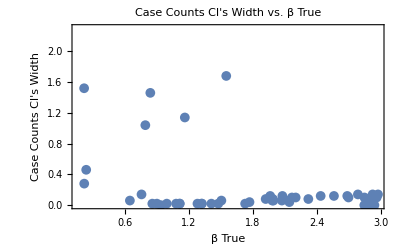

```mathematica
widthCasePlotAll
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report 2309/Figures/caseCI.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report 2309/Figures/caseCI.png

```mathematica
widthPhylo[intS_]:=CIWidth[{Min[ℒPCI[intS]],Max[ℒPCI[intS]]}]
```

```mathematica
widthPhyloPlotAll:=Module[{widthPhyloValues,betaValues},widthPhyloValues=Table[widthPhylo[Part[testTreeList,i]],{i,1,Length[testTreeList]}];
betaValues=Table[β/. testParsSIR2[testTreeList[[i]]],{i,1,Length[testTreeList]}];
ListPlot[Transpose[{betaValues,widthPhyloValues}],FrameLabel->{"β True","Phylogeny CI's Width"},PlotLabel->"Phylogeny CI's Width vs. β True",PlotRange->{All,{0,2.3}},PlotMarkers->{Automatic,Medium},PlotStyle->{Directive[col2]},Frame->True]]
```

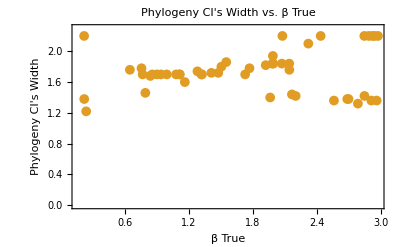

```mathematica
widthPhyloPlotAll
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report 2309/Figures/phyloCI.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report 2309/Figures/phyloCI.png

```mathematica
"/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/phyloCI.png"
```

```mathematica
Mean[1/CaseWidths]
```

3.01458

```mathematica
Mean[1/PhyloWidths]
```

0.629139

```mathematica
PrecCase[ints_]:=1/CIWidth[{Min[ℒCCI[ints]],Max[ℒCCI[ints]]}]
```

```mathematica
PrecCase[3]
```

0.649351

```mathematica
PrecPhylo[ints_]:=1/CIWidth[{Min[ℒPCI[ints]],Max[ℒPCI[ints]]}]
```

```mathematica
PrecPhylo[3]
```

0.806452

Plot of precision based on beta true values

```mathematica
PrCompPlot[intS_] := Block[{βTrue},
  βTrue = β /. testParsSIR2[intS];
  Show[
   (*Maximum Posterior Estimates*)
   ListPlot[{{{βTrue, PrecCase[intS]}}, {{βTrue, 
       PrecPhylo[intS]}}}, PlotMarkers -> {Automatic, Medium}, 
    PlotStyle -> {Automatic, Automatic, Red}],
   PlotRange -> {{0, 4}, {0, 4}}, 
   Epilog -> Inset[leg, Scaled[{0.9, 0.75}]], Frame -> True, 
   Axes -> False, FrameLabel->{"β true","Precision"},
   LabelStyle -> Directive[Black, Medium]]]
```

```mathematica
Show[Table[PrCompPlot[testTreeList[[j]]],{j,1,maxn(*Length[testTreeList]*)}]]
```

-Graphics-

Plot of precision based on tree size

```mathematica
PrCompPlotTree[intS_] := Block[{TreeSize},
  TreeSize = treeSize[intS];
  Show[
   (*Maximum Posterior Estimates*)
   ListPlot[{{{TreeSize, PrecCase[intS]}}, {{TreeSize, 
       PrecPhylo[intS]}}}, PlotMarkers -> {Automatic, Medium}, 
    PlotStyle -> {Automatic, Automatic, Red}],  PlotRange -> {{0, 100}, {0, 4}}, 
   Epilog -> Inset[leg, Scaled[{0.9, 0.75}]], Frame -> True, 
   Axes -> False,  FrameLabel->{"Tree Size","Precision"},
   LabelStyle -> Directive[Black, Medium]]]
```

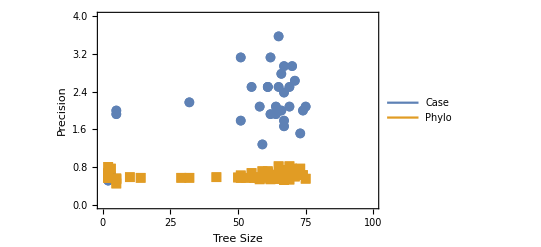

```mathematica
Show[Table[PrCompPlotTree[testTreeList[[j]]],{j,1,maxn(*Length[testTreeList]*)}]]
```

## Accuracy

```mathematica
AccuCaseSign[intS_]:=(β/. testParsSIR2[intS])-ℒCMPE[intS]
```

```mathematica
AccuPhyloSign[intS_]:=(β/. testParsSIR2[intS])-ℒPMPE[intS]
```

```mathematica
AccuCaseUnsign[intS_]:=Abs[(β/. testParsSIR2[intS])-ℒCMPE[intS]]
```

```mathematica
AccuPhyloUnsign[intS_]:=Abs[(β/. testParsSIR2[intS])-ℒPMPE[intS]]
```

```mathematica
RelErrorCase[intS_]:=Abs[((β/. testParsSIR2[intS])-ℒCMPE[intS])/(β/. testParsSIR2[intS])]
```

```mathematica
RelErrorPhylo[intS_]:=Abs[((β/. testParsSIR2[intS])-ℒPMPE[intS])/(β/. testParsSIR2[intS])]
```

```mathematica
(*Compute accuracies for each element of testTreeList*)
```

```mathematica
caseAccuracies=AccuCaseUnsign/@testTreeList;
```

```mathematica
phyloAccuracies=AccuPhyloUnsign/@testTreeList;
```

```mathematica
(*Combine the data*)
combinedData={caseAccuracies,phyloAccuracies};
```

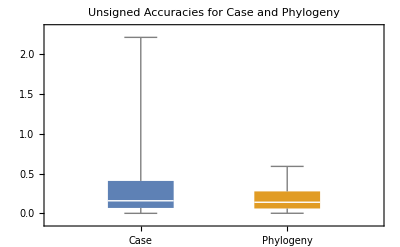

```mathematica
(*Make the box plot*)
BoxWhiskerChart[combinedData,ChartLabels->{"Case","Phylogeny"},ChartStyle->{Directive[col1],Directive[col2]},PlotLabel->"Unsigned Accuracies for Case and Phylogeny"]
```

Now, categorize iterations into low, medium and high beta

```mathematica
lowBetaList=Select[testTreeList,(β/. testParsSIR2[#])<1&];
mediumBetaList=Select[testTreeList,1<=(β/. testParsSIR2[#])<=2&];
highBetaList=Select[testTreeList,(β/. testParsSIR2[#])>2&];
```

```mathematica
lowBetaList
```

{26,31,32,33,37,38,56,60,71,74,90,99}

```mathematica
β/(γ+ψ)/. testParsSIR2[lowBetaList[[1]]]
```

1.65149

```mathematica
(β/(γ+ψ))/. testParsSIR2[#]&/@lowBetaList
```

{1.65149,0.389311,1.07367,1.31568,1.56053,0.356807,1.49675,1.25583,1.39381,1.2734,1.42493,0.358481}

```mathematica
mediumBetaList
```

{11,22,30,36,43,45,51,53,57,62,68,70,77,81,87,91,95,98}

```mathematica
β/. testParsSIR2[1]
```

2.41232

```mathematica
RelErrorCase[1]
```

0.243617

```mathematica
ℒCMPE[1]
```

3.

```mathematica
(ℒCMPE[1]-β/. testParsSIR2[1])/β/. testParsSIR2[1]
```

0.243617

Compute unsinged accuracies for each category (low, medium, high) for both cases and phylogenies.

```mathematica
caseAccuraciesLow=AccuCaseUnsign/@lowBetaList;
phyloAccuraciesLow=AccuPhyloUnsign/@lowBetaList;

caseAccuraciesMedium=AccuCaseUnsign/@mediumBetaList;
phyloAccuraciesMedium=AccuPhyloUnsign/@mediumBetaList;

caseAccuraciesHigh=AccuCaseUnsign/@highBetaList;
phyloAccuraciesHigh=AccuPhyloUnsign/@highBetaList;
```

Make the box plot for each category.

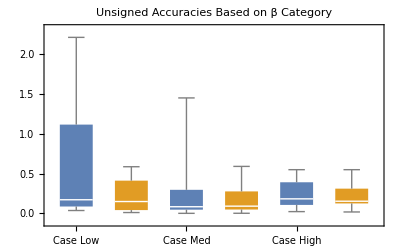

```mathematica
BoxWhiskerChart[{caseAccuraciesLow,phyloAccuraciesLow,caseAccuraciesMedium,phyloAccuraciesMedium,caseAccuraciesHigh,phyloAccuraciesHigh},ChartLabels->{"Case Low","Phylo Low","Case Med","Phylo Med","Case High","Phylo High"},ChartStyle->{Directive[col1],Directive[col2],Directive[col1],Directive[col2],Directive[col1],Directive[col2]},PlotLabel->"Unsigned Accuracies Based on β Category"]
```

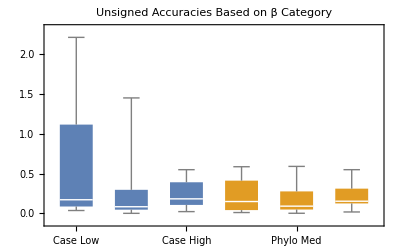

```mathematica
BoxWhiskerChart[{caseAccuraciesLow,caseAccuraciesMedium,caseAccuraciesHigh,phyloAccuraciesLow,phyloAccuraciesMedium,phyloAccuraciesHigh},ChartLabels->{"Case Low","Case Med","Case High","Phylo Low","Phylo Med","Phylo High"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Unsigned Accuracies Based on β Category"]
```

Compute signed accuracies for each category (low, medium, high) for both cases and phylogenies.

```mathematica
caseAccuraciesLowSign=AccuCaseSign/@lowBetaList;
phyloAccuraciesLowSign=AccuPhyloSign/@lowBetaList;

caseAccuraciesMediumSign=AccuCaseSign/@mediumBetaList;
phyloAccuraciesMediumSign=AccuPhyloSign/@mediumBetaList;

caseAccuraciesHighSign=AccuCaseSign/@highBetaList;
phyloAccuraciesHighSign=AccuPhyloSign/@highBetaList;
```

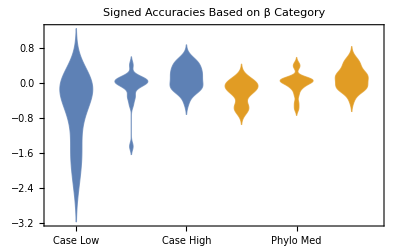

```mathematica
DistributionChart[{caseAccuraciesLowSign,caseAccuraciesMediumSign,caseAccuraciesHighSign,phyloAccuraciesLowSign,phyloAccuraciesMediumSign,phyloAccuraciesHighSign},ChartLabels->{"Case Low","Case Med","Case High","Phylo Low","Phylo Med","Phylo High"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Signed Accuracies Based on β Category"]
```

Compute relative error for each beta category (low, medium, high) for both cases and phylogenies.

```mathematica
caseRelErrorLow=RelErrorCase/@lowBetaList;
phyloRelErrorLow=RelErrorPhylo/@lowBetaList;

caseRelErrorMedium=RelErrorCase/@mediumBetaList;
phyloRelErrorMedium=RelErrorPhylo/@mediumBetaList;

caseRelErrorHigh=RelErrorCase/@highBetaList;
phyloRelErrorHigh=RelErrorPhylo/@highBetaList;
```

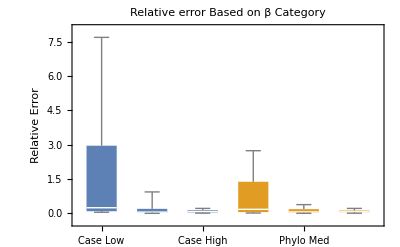

```mathematica
BoxWhiskerChart[{caseRelErrorLow,caseRelErrorMedium,caseRelErrorHigh,phyloRelErrorLow,phyloRelErrorMedium,phyloRelErrorHigh},ChartLabels->{"Case Low","Case Med","Case High","Phylo Low","Phylo Med","Phylo High"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Relative error Based on β Category",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,10}}]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/relErrorBeta.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/relErrorBeta.png

Plot based on tree size

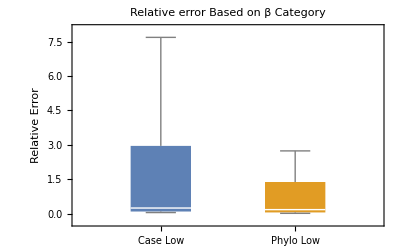

```mathematica
BoxWhiskerChart[{caseRelErrorLow,phyloRelErrorLow},ChartLabels->{"Case Low","Phylo Low"},ChartStyle->{Directive[col1],Directive[col2]},PlotLabel->"Relative error Based on β Category",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,10}}]
```

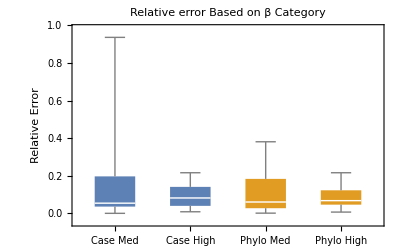

```mathematica
BoxWhiskerChart[{caseRelErrorMedium,caseRelErrorHigh,phyloRelErrorMedium,phyloRelErrorHigh},ChartLabels->{"Case Med","Case High","Phylo Med","Phylo High"},ChartStyle->{Directive[col1],Directive[col1],Directive[col2],Directive[col2]},PlotLabel->"Relative error Based on β Category",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,10}}]
```

```mathematica
treeSize/@testTreeList
```

{695,669,649,651,643,656,673,580,642,219,646,2,14,2,651,645,614,166,2,655,555,640,633,667,604,286,620,13,649,496,679,672,529,656,3,3,656,30,388,632,631,2,658,646,301,562,608,667,424,4}

```mathematica
smallTreeList=Select[testTreeList,treeSize[#]<20&];
mediumTreeList=Select[testTreeList,20<=treeSize[#]<=500&];
largeTreeList=Select[testTreeList,treeSize[#]>500&];
```

Compute unsinged accuracies for each category of tree sizes (small, medium, large) for both cases and phylogenies.

```mathematica
smallTreeList
```

{31,32,33,38,60,70,71,87,99}

```mathematica
mediumTreeList
```

{26,37,56,62,74,77,90,98}

```mathematica
largeTreeList
```

{4,7,8,10,11,16,20,22,25,30,34,35,36,42,43,45,51,52,53,57,61,63,64,68,69,72,79,81,88,89,91,95,96}

```mathematica
caseAccuraciesSmall=AccuCaseUnsign/@smallTreeList;
phyloAccuraciesSmall=AccuPhyloUnsign/@smallTreeList;

caseAccuraciesMediumTree=AccuCaseUnsign/@mediumTreeList;
phyloAccuraciesMediumTree=AccuPhyloUnsign/@mediumTreeList;

caseAccuraciesLarge=AccuCaseUnsign/@largeTreeList;
phyloAccuraciesLarge=AccuPhyloUnsign/@largeTreeList;
```

Make the box plot for each category .

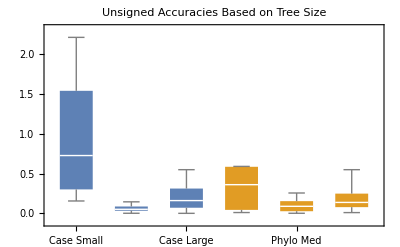

```mathematica
BoxWhiskerChart[{caseAccuraciesSmall,caseAccuraciesMediumTree,caseAccuraciesLarge,phyloAccuraciesSmall,phyloAccuraciesMediumTree,phyloAccuraciesLarge},ChartLabels->{"Case Small","Case Med","Case Large","Phylo Small","Phylo Med","Phylo Large"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Unsigned Accuracies Based on Tree Size"]
```

Compute signed accuracies for each tree size category (small, medium, large) for both cases and phylogenies .

```mathematica
caseAccuraciesSmallSign=AccuCaseSign/@smallTreeList;
phyloAccuraciesSmallSign=AccuPhyloSign/@smallTreeList;

caseAccuraciesMediumTreeSign=AccuCaseSign/@mediumTreeList;
phyloAccuraciesMediumTreeSign=AccuPhyloSign/@mediumTreeList;

caseAccuraciesLargeSign=AccuCaseSign/@largeTreeList;
phyloAccuraciesLargeSign=AccuPhyloSign/@largeTreeList;
```

Distribution plot for tree size

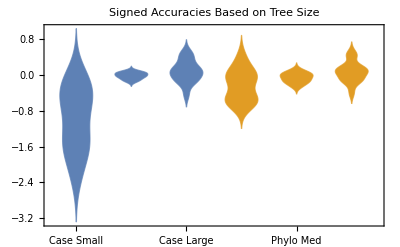

```mathematica
DistributionChart[{caseAccuraciesSmallSign,caseAccuraciesMediumTreeSign,caseAccuraciesLargeSign,phyloAccuraciesSmallSign,phyloAccuraciesMediumTreeSign,phyloAccuraciesLargeSign},ChartLabels->{"Case Small","Case Med","Case Large","Phylo Small","Phylo Med","Phylo Large"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Signed Accuracies Based on Tree Size"]
```

Compute relative error for each tree size category (small, medium, large) for both cases and phylogenies .

```mathematica
caseRelErrorSmall=RelErrorCase/@smallTreeList;
phyloRelErrorSmall=RelErrorPhylo/@smallTreeList;

caseRelErrorMediumTree=RelErrorCase/@mediumTreeList;
phyloRelErrorMediumTree=RelErrorPhylo/@mediumTreeList;

caseRelErrorLarge=RelErrorCase/@largeTreeList;
phyloRelErrorLarge=RelErrorPhylo/@largeTreeList;
```

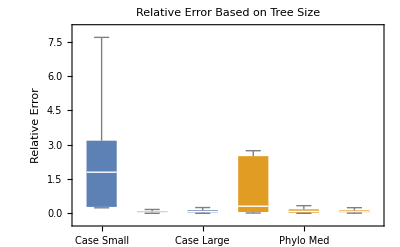

```mathematica
BoxWhiskerChart[{caseRelErrorSmall,caseRelErrorMediumTree,caseRelErrorLarge,phyloRelErrorSmall,phyloRelErrorMediumTree,phyloRelErrorLarge},ChartLabels->{"Case Small","Case Med","Case Large","Phylo Small","Phylo Med","Phylo Large"},ChartStyle->{Directive[col1],Directive[col1],Directive[col1],Directive[col2],Directive[col2],Directive[col2]},PlotLabel->"Relative Error Based on Tree Size",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,9}}]
```

```mathematica
Export["/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/relErrorTree.png",%]
```

/Users/siavashriazi/Dropbox/Apps/Overleaf/SR Report/Figures/relErrorTree.png

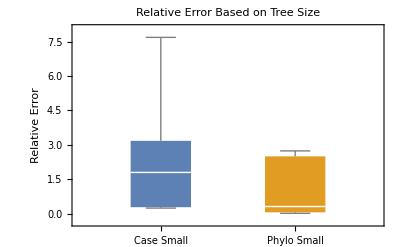

```mathematica
BoxWhiskerChart[{caseRelErrorSmall,phyloRelErrorSmall},ChartLabels->{"Case Small","Phylo Small"},ChartStyle->{Directive[col1],Directive[col2]},PlotLabel->"Relative Error Based on Tree Size",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,9}}]
```

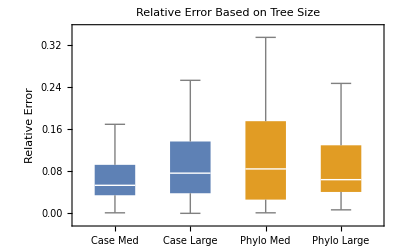

```mathematica
BoxWhiskerChart[{caseRelErrorMediumTree,caseRelErrorLarge,phyloRelErrorMediumTree,phyloRelErrorLarge},ChartLabels->{"Case Med","Case Large","Phylo Med","Phylo Large"},ChartStyle->{Directive[col1],Directive[col1],Directive[col2],Directive[col2]},PlotLabel->"Relative Error Based on Tree Size",FrameLabel->{{"Relative Error",None},{None,None}},LabelStyle->{Automatic,{Medium,9}}]
```

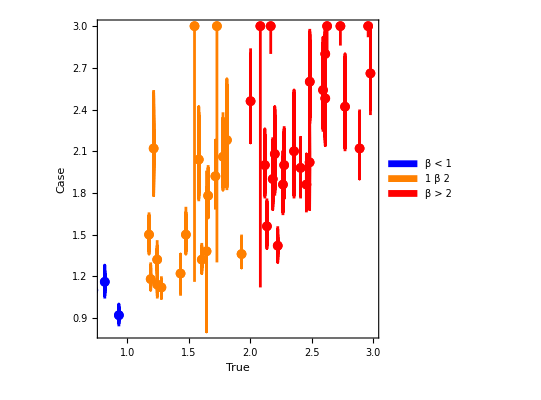

```mathematica
CICasePlotCat[intS_]:=Block[{βTrue,βRange},βTrue=β/. testParsSIR2[intS];
βRange=βTrue;
Module[{color},If[βRange<1,color=Blue,If[1<=βRange<=2,color=Orange,color=Red]];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[color,Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->(Directive[color,Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Case"},LabelStyle->Directive[Black,Medium],Epilog->Inset[SwatchLegend[{Blue,Orange,Red},{"β < 1","1  β  2","β > 2"}],Scaled[{0.9,0.1}]]]]]

Show[Table[CICasePlotCat[testTreeList[[j]]],{j,1,maxn}]]
```

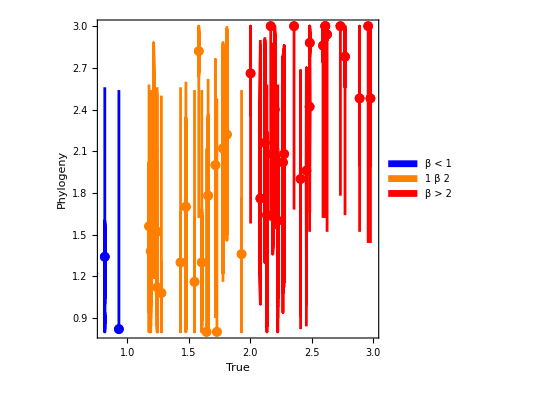

```mathematica
CIPhyloPlotCat[intS_]:=Block[{βTrue,βRange},βTrue=β/. testParsSIR2[intS];
βRange=βTrue;
Module[{color},If[βRange<1,color=Blue,If[1<=βRange<=2,color=Orange,color=Red]];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒPMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[color,Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->(Directive[color,Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Phylogeny"},LabelStyle->Directive[Black,Medium],Epilog->Inset[SwatchLegend[{Blue,Orange,Red},{"β < 1","1  β  2","β > 2"}],Scaled[{0.9,0.1}]]]]]

Show[Table[CIPhyloPlotCat[testTreeList[[j]]],{j,1,maxn}]]
```

General::munfl: 0.02 7.72935013179119×10^-691 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 1.145354482968×10^-657 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.02 2.86875410398211×10^-625 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

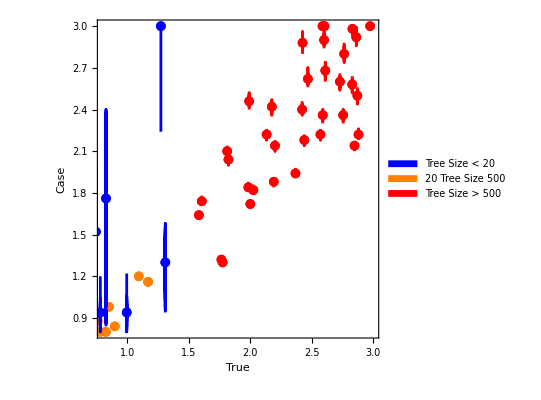

```mathematica
CICasePlotCatTree[intS_]:=Block[{βTrue,βRange,treeSizeCategory},βTrue=β/. testParsSIR2[intS];
βRange=βTrue;
treeSizeCategory=Which[treeSize[intS]<20,"Small",20<=treeSize[intS]<=500,"Medium",treeSize[intS]>500,"Large"];
Module[{color},Switch[treeSizeCategory,"Small",color=Blue,"Medium",color=Orange,"Large",color=Red];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒCMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[color,Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒCCI[intS]]},AspectRatio->1,PlotStyle->(Directive[color,Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Case"},LabelStyle->Directive[Black,Medium],Epilog->Inset[SwatchLegend[{Blue,Orange,Red},{"Tree Size < 20","20  Tree Size  500","Tree Size > 500"}],Scaled[{0.82,0.1}]]]]]

Show[Table[CICasePlotCatTree[testTreeList[[j]]],{j,1,maxn}]]
```

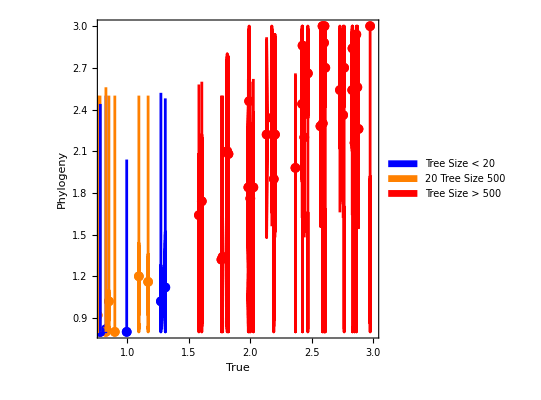

```mathematica
CIPhyloPlotCatTree[intS_]:=Block[{βTrue,βRange,treeSizeCategory},βTrue=β/. testParsSIR2[intS];
βRange=βTrue;
treeSizeCategory=Which[treeSize[intS]<20,"Small",20<=treeSize[intS]<=500,"Medium",treeSize[intS]>500,"Large"];
Module[{color},Switch[treeSizeCategory,"Small",color=Blue,"Medium",color=Orange,"Large",color=Red];
Show[(*Maximum Posterior Estimates*)ListPlot[{{{βTrue,ℒPMPE[intS]}}},PlotMarkers->{Graphics[{EdgeForm[],Disk[]}],Medium},PlotStyle->(Directive[color,Opacity[1]])],(*Credible Intervals*)ListLinePlot[{Map[{βTrue,#}&,ℒPCI[intS]]},AspectRatio->1,PlotStyle->(Directive[color,Opacity[1]])],AspectRatio->1,PlotRange->{{0.8,3},{0.8,3}},Frame->True,Axes->False,FrameLabel->{" True","  Phylogeny"},LabelStyle->Directive[Black,Medium],Epilog->Inset[SwatchLegend[{Blue,Orange,Red},{"Tree Size < 20","20  Tree Size  500","Tree Size > 500"}],Scaled[{0.2,0.9}]]]]]

Show[Table[CIPhyloPlotCatTree[testTreeList[[j]]],{j,1,maxn}]]
```